```mathematica
Clear["Global`*"]
SetDirectory[FileNameJoin[{NotebookDirectory[],"../figs/"}]]
```

/Users/marknovak/Git/aaaManuscripts/GeometricComplexity/figs

SC_2= -Log_ef(x|(Θ̂)_x)+k/2 Log_e(n/(2 π))+Log_e∫_Θ √(det I(Θ))ⅆΘ + o(1);
The first term is the likelihood. The second term is the parameter and sample size dependent component.
The third term containing I(Θ), the Expected Fisher Information Matrix, reflects the model's flexibility.

### Second Term dependence on k and n

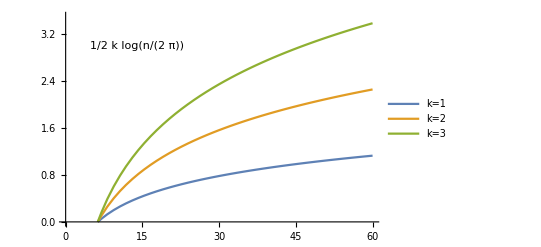
-Graphics-Sample size (n)Parameter complexity

```mathematica
AltLabel1="k";
p1=Labeled[
Plot[
Evaluate@Table[k/2 Log[n/(2 π)],{k,1,3}],{n,1,60},
PlotRange->{{0,60},{0,3.5}},
PlotLegends->Placed[{"k=1","k=2","k=3"},Above],
Epilog->Text[k/2 Log[n/(2 π)],{14,3}]
],
{Style["Sample size (n)"],
Style["Parameter complexity"]},
{Bottom,Left},
RotateLabel->True,
Spacings->{1, 0},
BaseStyle->{FontFamily->"Arial",12},
LabelStyle->{FontFamily->"Arial"},
ImageSize->Medium
]
Export["ParamComp_2ndTerm.pdf",p1];
```